```mathematica
(*THIS MATH AND PHYSICS NEEDS SOME RIGID BODY PHYSICS PROBABLY*)
ClearAll["Global`*"]
x1[t_] :=r1*-Sin[a1[t]];
y1[t_]:=r1*Cos[a1[t]];
x[t_] := r1*-Sin[a1[t]]+r2*-Sin[a1[t]+a2[t]];
y[t_] := r1*Cos[a1[t]]+r2*Cos[a1[t]+a2[t]];
```

```mathematica
T = Simplify[TrigReduce[1/2*(m1(x1'[t]^2+y1'[t]^2)+m2(x'[t]^2+y'[t]^2))]]
```

1/2 ((m1 r1^2+m2 (r1^2+r2^2)+2 m2 r1 r2 Cos[a2[t]]) a1'[t]^2+2 m2 r2 (r2+r1 Cos[a2[t]]) a1'[t] a2'[t]+m2 r2^2 a2'[t]^2)

```mathematica
k = {k1, k2, k3, k4};
ra = {ra1, ra2};
friction = {fr1, fr2};
Lang = {{d11, d12},{d21, d22},{d31,d32}, {d41,d42}};
initDef = {def1, def2, def3, def4};
```

```mathematica
V = 1/2*(k[[1]]*(Lang[[1,1]]*a1[t]*ra[[1]]+Lang[[1,2]]*(a2[t])*ra[[2]]+initDef[[1]])^2+
k[[2]]*(Lang[[2,1]]*a1[t]*ra[[1]]+Lang[[2,2]]*(a2[t])*ra[[2]]+initDef[[2]])^2+
k[[3]]*(Lang[[3,1]]*a1[t]*ra[[1]]+Lang[[3,2]]*(a2[t])*ra[[2]]+initDef[[3]])^2+ 
k[[4]]*(Lang[[4,1]]*a1[t]*ra[[1]]+Lang[[4,2]]*(a2[t])*ra[[2]]+initDef[[4]])^2)
```

1/2 (k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])^2+k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])^2+k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])^2+k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t])^2)

```mathematica
Fr =  1/2*(friction[[1]]*a1'[t]^2+ friction[[2]]*a2'[t]^2 )
```

1/2 (fr1 a1'[t]^2+fr2 a2'[t]^2)

```mathematica
L = T-V
H = T+V
TotEng = T+V+Fr
```

1/2 (-k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])^2-k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])^2-k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])^2-k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t])^2)+1/2 ((m1 r1^2+m2 (r1^2+r2^2)+2 m2 r1 r2 Cos[a2[t]]) a1'[t]^2+2 m2 r2 (r2+r1 Cos[a2[t]]) a1'[t] a2'[t]+m2 r2^2 a2'[t]^2)

1/2 (k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])^2+k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])^2+k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])^2+k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t])^2)+1/2 ((m1 r1^2+m2 (r1^2+r2^2)+2 m2 r1 r2 Cos[a2[t]]) a1'[t]^2+2 m2 r2 (r2+r1 Cos[a2[t]]) a1'[t] a2'[t]+m2 r2^2 a2'[t]^2)

1/2 (k1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])^2+k2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])^2+k3 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])^2+k4 (def4+d41 ra1 a1[t]+d42 ra2 a2[t])^2)+1/2 (fr1 a1'[t]^2+fr2 a2'[t]^2)+1/2 ((m1 r1^2+m2 (r1^2+r2^2)+2 m2 r1 r2 Cos[a2[t]]) a1'[t]^2+2 m2 r2 (r2+r1 Cos[a2[t]]) a1'[t] a2'[t]+m2 r2^2 a2'[t]^2)

```mathematica
a1Solve = D[D[L,a1'[t]],t]==D[L,a1[t]]-D[Fr,a1'[t]]
a2Solve = D[D[L,a2'[t]],t]==D[L,a2[t]]-D[Fr,a2'[t]]
```

1/2 (-4 m2 r1 r2 Sin[a2[t]] a1'[t] a2'[t]-2 m2 r1 r2 Sin[a2[t]] a2'[t]^2+2 (m1 r1^2+m2 (r1^2+r2^2)+2 m2 r1 r2 Cos[a2[t]]) a1''[t]+2 m2 r2 (r2+r1 Cos[a2[t]]) a2''[t])==1/2 (-2 d11 k1 ra1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])-2 d21 k2 ra1 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])-2 d31 k3 ra1 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])-2 d41 k4 ra1 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]))-fr1 a1'[t]

1/2 (-2 m2 r1 r2 Sin[a2[t]] a1'[t] a2'[t]+2 m2 r2 (r2+r1 Cos[a2[t]]) a1''[t]+2 m2 r2^2 a2''[t])==1/2 (-2 d12 k1 ra2 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])-2 d22 k2 ra2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])-2 d32 k3 ra2 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])-2 d42 k4 ra2 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]))-fr2 a2'[t]+1/2 (-2 m2 r1 r2 Sin[a2[t]] a1'[t]^2-2 m2 r1 r2 Sin[a2[t]] a1'[t] a2'[t])

```mathematica
sol = Solve[{a1Solve, a2Solve}, {a1''[t], a2''[t]}][[1]]
(*a2sol = Simplify[TrigReduce[Solve[a2Solve, a2''[t]][[1]]]]*)
```

{a1''[t]→-((m2 r2^2 (1/2 (2 d11 k1 ra1 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])+2 d21 k2 ra1 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])+2 d31 k3 ra1 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])+2 d41 k4 ra1 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]))+fr1 a1'[t]-2 m2 r1 r2 Sin[a2[t]] a1'[t] a2'[t]-m2 r1 r2 Sin[a2[t]] a2'[t]^2)-m2 r2 (r2+r1 Cos[a2[t]]) (1/2 (2 d12 k1 ra2 (def1+d11 ra1 a1[t]+d12 ra2 a2[t])+2 d22 k2 ra2 (def2+d21 ra1 a1[t]+d22 ra2 a2[t])+2 d32 k3 ra2 (def3+d31 ra1 a1[t]+d32 ra2 a2[t])+2 d42 k4 ra2 (def4+d41 ra1 a1[t]+d42 ra2 a2[t]))+fr2 a2'[t]-m2 r1 r2 Sin[a2[t]] a1'[t] a2'[t]+1/2 (2 m2 r1 r2 Sin[a2[t]] a1'[t]^2+2 m2 r1 r2 Sin[a2[t]] a1'[t] a2'[t])))/(m1 m2 r1^2 r2^2+m2^2 r1^2 r2^2-m2^2 r1^2 r2^2 Cos[a2[t]]^2)),a2''[t]→-1/(m2 r1^2 r2^2 (-m1-m2+m2 Cos[a2[t]]^2))(d11 def1 k1 m2 r2^2 ra1+d21 def2 k2 m2 r2^2 ra1+d31 def3 k3 m2 r2^2 ra1+d41 def4 k4 m2 r2^2 ra1-d12 def1 k1 m1 r1^2 ra2-d22 def2 k2 m1 r1^2 ra2-d32 def3 k3 m1 r1^2 ra2-d42 def4 k4 m1 r1^2 ra2-d12 def1 k1 m2 r1^2 ra2-d22 def2 k2 m2 r1^2 ra2-d32 def3 k3 m2 r1^2 ra2-d42 def4 k4 m2 r1^2 ra2-d12 def1 k1 m2 r2^2 ra2-d22 def2 k2 m2 r2^2 ra2-d32 def3 k3 m2 r2^2 ra2-d42 def4 k4 m2 r2^2 ra2+d11^2 k1 m2 r2^2 ra1^2 a1[t]+d21^2 k2 m2 r2^2 ra1^2 a1[t]+d31^2 k3 m2 r2^2 ra1^2 a1[t]+d41^2 k4 m2 r2^2 ra1^2 a1[t]-d11 d12 k1 m1 r1^2 ra1 ra2 a1[t]-d21 d22 k2 m1 r1^2 ra1 ra2 a1[t]-d31 d32 k3 m1 r1^2 ra1 ra2 a1[t]-d41 d42 k4 m1 r1^2 ra1 ra2 a1[t]-d11 d12 k1 m2 r1^2 ra1 ra2 a1[t]-d21 d22 k2 m2 r1^2 ra1 ra2 a1[t]-d31 d32 k3 m2 r1^2 ra1 ra2 a1[t]-d41 d42 k4 m2 r1^2 ra1 ra2 a1[t]-d11 d12 k1 m2 r2^2 ra1 ra2 a1[t]-d21 d22 k2 m2 r2^2 ra1 ra2 a1[t]-d31 d32 k3 m2 r2^2 ra1 ra2 a1[t]-d41 d42 k4 m2 r2^2 ra1 ra2 a1[t]+d11 d12 k1 m2 r2^2 ra1 ra2 a2[t]+d21 d22 k2 m2 r2^2 ra1 ra2 a2[t]+d31 d32 k3 m2 r2^2 ra1 ra2 a2[t]+d41 d42 k4 m2 r2^2 ra1 ra2 a2[t]-d12^2 k1 m1 r1^2 ra2^2 a2[t]-d22^2 k2 m1 r1^2 ra2^2 a2[t]-d32^2 k3 m1 r1^2 ra2^2 a2[t]-d42^2 k4 m1 r1^2 ra2^2 a2[t]-d12^2 k1 m2 r1^2 ra2^2 a2[t]-d22^2 k2 m2 r1^2 ra2^2 a2[t]-d32^2 k3 m2 r1^2 ra2^2 a2[t]-d42^2 k4 m2 r1^2 ra2^2 a2[t]-d12^2 k1 m2 r2^2 ra2^2 a2[t]-d22^2 k2 m2 r2^2 ra2^2 a2[t]-d32^2 k3 m2 r2^2 ra2^2 a2[t]-d42^2 k4 m2 r2^2 ra2^2 a2[t]+d11 def1 k1 m2 r1 r2 ra1 Cos[a2[t]]+d21 def2 k2 m2 r1 r2 ra1 Cos[a2[t]]+d31 def3 k3 m2 r1 r2 ra1 Cos[a2[t]]+d41 def4 k4 m2 r1 r2 ra1 Cos[a2[t]]-2 d12 def1 k1 m2 r1 r2 ra2 Cos[a2[t]]-2 d22 def2 k2 m2 r1 r2 ra2 Cos[a2[t]]-2 d32 def3 k3 m2 r1 r2 ra2 Cos[a2[t]]-2 d42 def4 k4 m2 r1 r2 ra2 Cos[a2[t]]+d11^2 k1 m2 r1 r2 ra1^2 a1[t] Cos[a2[t]]+d21^2 k2 m2 r1 r2 ra1^2 a1[t] Cos[a2[t]]+d31^2 k3 m2 r1 r2 ra1^2 a1[t] Cos[a2[t]]+d41^2 k4 m2 r1 r2 ra1^2 a1[t] Cos[a2[t]]-2 d11 d12 k1 m2 r1 r2 ra1 ra2 a1[t] Cos[a2[t]]-2 d21 d22 k2 m2 r1 r2 ra1 ra2 a1[t] Cos[a2[t]]-2 d31 d32 k3 m2 r1 r2 ra1 ra2 a1[t] Cos[a2[t]]-2 d41 d42 k4 m2 r1 r2 ra1 ra2 a1[t] Cos[a2[t]]+d11 d12 k1 m2 r1 r2 ra1 ra2 a2[t] Cos[a2[t]]+d21 d22 k2 m2 r1 r2 ra1 ra2 a2[t] Cos[a2[t]]+d31 d32 k3 m2 r1 r2 ra1 ra2 a2[t] Cos[a2[t]]+d41 d42 k4 m2 r1 r2 ra1 ra2 a2[t] Cos[a2[t]]-2 d12^2 k1 m2 r1 r2 ra2^2 a2[t] Cos[a2[t]]-2 d22^2 k2 m2 r1 r2 ra2^2 a2[t] Cos[a2[t]]-2 d32^2 k3 m2 r1 r2 ra2^2 a2[t] Cos[a2[t]]-2 d42^2 k4 m2 r1 r2 ra2^2 a2[t] Cos[a2[t]]+fr1 m2 r2^2 a1'[t]+fr1 m2 r1 r2 Cos[a2[t]] a1'[t]-m1 m2 r1^3 r2 Sin[a2[t]] a1'[t]^2-m2^2 r1^3 r2 Sin[a2[t]] a1'[t]^2-m2^2 r1 r2^3 Sin[a2[t]] a1'[t]^2-2 m2^2 r1^2 r2^2 Cos[a2[t]] Sin[a2[t]] a1'[t]^2-fr2 m1 r1^2 a2'[t]-fr2 m2 r1^2 a2'[t]-fr2 m2 r2^2 a2'[t]-2 fr2 m2 r1 r2 Cos[a2[t]] a2'[t]-2 m2^2 r1 r2^3 Sin[a2[t]] a1'[t] a2'[t]-2 m2^2 r1^2 r2^2 Cos[a2[t]] Sin[a2[t]] a1'[t] a2'[t]-m2^2 r1 r2^3 Sin[a2[t]] a2'[t]^2-m2^2 r1^2 r2^2 Cos[a2[t]] Sin[a2[t]] a2'[t]^2)}

```mathematica
(*THIS SYSTEM ASSUMES MASS IS AT TIP OF FINGER OBJECT*)
```

```mathematica
parameters = {
m1->1,
m2->1,

r1->1/20, 
r2->1/40,

k1->100,
k2->100,
k3->100,
k4->100,

fr1->1/50,
fr2->1/50,

ra1->1/50,
ra2->1/50,

d11->-1, d12->-1,
d21->1, d22->1,
d31->-1, d32->1,
d41->1, d42->-1,
(*-1 means clockwise, 1 means counter clockwise, 0 means no effect*)

def1->.05,
def2->.15,
def3->.2,
def4->.02};
soltime = 5;
```

```mathematica
governingEq1 = a1''[t]==(a1''[t]/.sol)/.parameters;
governingEq2 = a2''[t] == (a2''[t] /.sol)/.parameters;

(*NOTE: Don't use this --> Method->{"EquationSimplification"->"Residual"};
It is restrictive whereas not setting it uses multiple methods for simplification.*)
(*s = NDSolve[{governingEq1,a1[0]==0, a1'[0]== 0},a1[t],{t,0,soltime}]*)
s = NDSolve[{governingEq1, governingEq2,a1[0]==.01, a1'[0]== 0, a2[0]==0.01, a2'[0]==0},{a1[t],a2[t]},{t,0,soltime}];
finsol = {s[[1,1]],s[[1,2]],D[s,t][[1,1]],D[s,t][[1,2]], D[s,{t,2}][[1,1]], D[s,{t,2}][[1,2]]};
(*s2 =  NDSolve[{governingEq1, governingEq2,a1[0]==0, a1'[0]== 0, a2[0]==0, a2'[0]==0},a2[t],{t,0,soltime} ,Method->{"EquationSimplification"->"Residual"}]*)
```

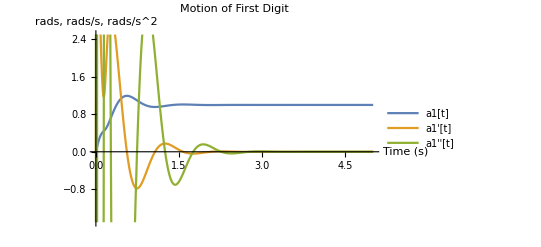

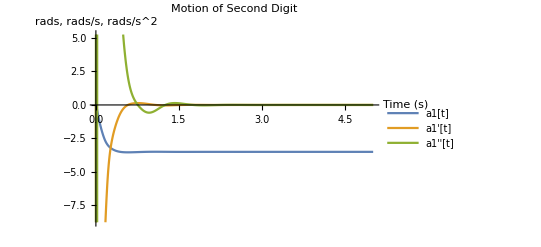

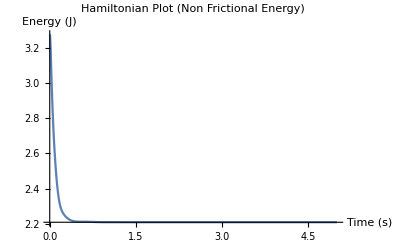

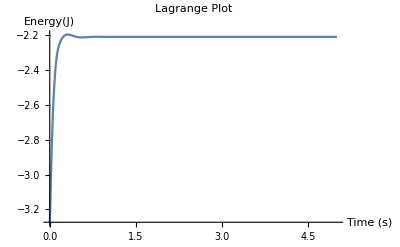

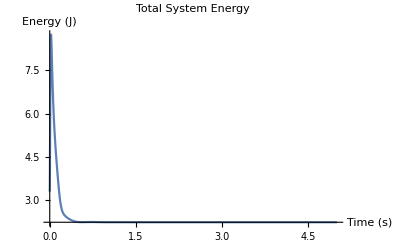

```mathematica
Plot[{a1[t]/.finsol, a1'[t]/.finsol, a1''[t]/.finsol},{t,0,soltime},PlotLabel->"Motion of First Digit", PlotLegends->{"a1[t]", "a1'[t]", "a1''[t]"},AxesLabel->{"Time (s)","rads, rads/s, rads/s^2"}, PlotRange->Automatic]
Plot[{a2[t]/.finsol, a2'[t]/.finsol, a2''[t]/.finsol},{t,0,soltime},PlotLabel->"Motion of Second Digit", PlotLegends->{"a1[t]", "a1'[t]", "a1''[t]"},AxesLabel->{"Time (s)","rads, rads/s, rads/s^2"}, PlotRange->Automatic]
Plot[Evaluate[H/.parameters/.finsol],{t,0,soltime},PlotLabel->"Hamiltonian Plot (Non Frictional Energy)",AxesLabel->{"Time (s)","Energy (J)"},PlotRange->Full]
Plot[Evaluate[L/.parameters/.finsol],{t,0,soltime},PlotLabel->"Lagrange Plot",AxesLabel->{"Time (s)","Energy(J)"}, PlotRange->Full]
Plot[Evaluate[TotEng/.parameters/.finsol],{t,0,soltime},PlotLabel->"Total System Energy",AxesLabel->{"Time (s)","Energy (J)"}, PlotRange->Full]
```

```mathematica
(*ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s[[1]]],{t,0,soltime},PlotRange->{{-.15,.15},{-.15,.15}},AxesLabel-> {"î","ĵ"}]
ParametricPlot[Evaluate[{x1[t],y1[t]}/.parameters/.s[[1]]],{t,0,soltime},PlotRange->{{-.15,.15},{-.15,.15}},AxesLabel-> {"î","ĵ"}]*)
```

```mathematica
(*{{0,0},{x1[t],1},{2,2}}/.parameters/.finsol/.{t->t0}*)
```

```mathematica
tailLen = .2;
Animate[Show[{
ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s],{t,0,t0},AxesOrigin->{0,0},PlotRange->{{-.1,.1},{-.1, .1}},AspectRatio->1,ImageSize->500, PlotStyle->{Orange},AxesLabel-> {"X","Y"}],
ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s],{t,Max[t0-tailLen,0],t0},AxesOrigin->{0,0},PlotRange->{{-.1,.1},{-.1, .1}},AspectRatio->1,ImageSize->500, PlotStyle->{Red,Thick},AxesLabel-> {"X","Y"}],

ParametricPlot[Evaluate[{x1[t],y1[t]}/.parameters/.s],{t,0,t0},AxesOrigin->{0,0},PlotRange->{{-.1,.1},{-.1, .1}},AspectRatio->1,ImageSize->500, PlotStyle->{Blue},AxesLabel-> {"X","Y"}],
ParametricPlot[Evaluate[{x1[t],y1[t]}/.parameters/.s],{t,Max[t0-tailLen,0],t0},AxesOrigin->{0,0},PlotRange->{{-.1,.1},{-.1, .1}},AspectRatio->1,ImageSize->500, PlotStyle->{Red,Thick},AxesLabel-> {"X","Y"}],
Graphics[{Thick, Line[Evaluate[{{0,0},{x1[t],y1[t]},{x[t],y[t]}}/.parameters/.finsol/.{t->t0}]]}]
}],{t0, 0 ,soltime}, AnimationRate->.1]
```